# Метод на разполовяването

Задача 1: Дадено е уравенението:
(a - 9x)/(x^2 + b + 1) - x^2 + (2a + 1)sinx + a + b = 0, където а е предпоследната цифра на факултетния ни номер, а b  последната.
=> (6 - 9x)/(x^2 + 8) - x^2 + 13sinx + 13 = 0;
1. Представете геометрична интерпретация на уравнението.
2. Да се локализира един от корените.
3. Уточнете локализирания корен по метода на разполовяването.
4. Оценка на грешката.
5. Колко биха били броя на итерациите за достигане на точност 0.0001 по метода на разполовяването, използвайки интервала от локализацията на корена.

```mathematica
f[x_]:=  (6 - 9x)/(x^2 + 8) - x^2 + 13Sin[x] + 13
```

```mathematica
f[x]
```

13-x^2+(6-9 x)/(8+x^2)+13 Sin[x]

## 1. Визуализация на функцията

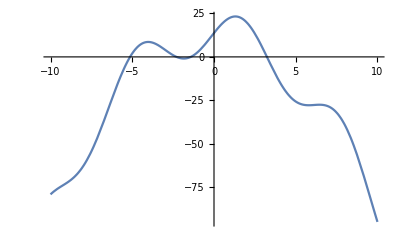

```mathematica
Plot[f[x],{x,-10,10}]
```

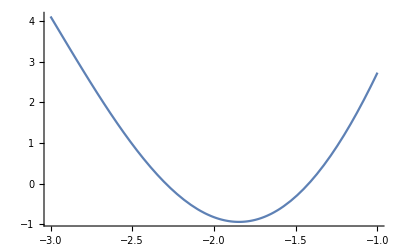

```mathematica
Plot[f[x],{x,-3,-1}]
```

## 2. Да се локализира един от корените.

Локализираме най-големия корен

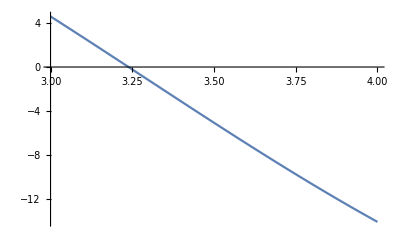

```mathematica
Plot[f[x],{x,3,4}]
```

```mathematica
f[3.]
```

4.59927

```mathematica
f[4.]
```

-14.0884

Извод:
(1) Функцията е непрекъсната, защото е сума от непрекъснати функции (полином и синус)
(2) f(3) = 4.59927... > 0
       f(4) = -14.0884... < 0
       => Функцията има различни знаци в двата края на разглеждания интервал [3; 4].
       От (1) и (2) следва, че функцията има поне един корен в разглеждания интервал [3; 4].

## 3. Уточнете локализирания корен по метода на разполовяването.

```mathematica
f[x_]:=  (6 - 9x)/(x^2 + 8) - x^2 + 13Sin[x] + 13
a =  3.;b = 4.;
For[n = 0, n <6 , n++, 
Print["n = ",n, " a_n = ",a, " b_n = ",b, " m_n = ",m =  (a + b)/2  ,  " f(m_n) = ",f[m], " ε_n = ", (b - a)/2];
If[f[m] > 0, b = m, a = m]
]
```

n = 0 a_n = 3. b_n = 4. m_n = 3.5 f(m_n) = -5.06944 ε_n = 0.5

n = 1 a_n = 3.5 b_n = 4. m_n = 3.75 f(m_n) = -9.75059 ε_n = 0.25

n = 2 a_n = 3.75 b_n = 4. m_n = 3.875 f(m_n) = -11.9725 ε_n = 0.125

n = 3 a_n = 3.875 b_n = 4. m_n = 3.9375 f(m_n) = -13.0448 ε_n = 0.0625

n = 4 a_n = 3.9375 b_n = 4. m_n = 3.96875 f(m_n) = -13.5704 ε_n = 0.03125

n = 5 a_n = 3.96875 b_n = 4. m_n = 3.98438 f(m_n) = -13.8304 ε_n = 0.015625

## 4. Оценка на грешката.

Цикъл при достигане на определена предварително зададена точност (със стоп-критерий):

```mathematica
f[x_]:=  (6 - 9x)/(x^2 + 8) - x^2 + 13Sin[x] + 13
a =  3.;b = 4.;
epszad = 0.00000001;
eps =  Infinity;
For[n = 0, eps > epszad , n++, 
Print["n = ",n, " a_n = ",a, " b_n = ",b, " m_n = ",m =  (a + b)/2  ,  " f(m_n) = ",f[m], " ε_n = ", eps = (b - a)/2];
If[f[m] > 0, b = m, a = m]
]
```

n = 0 a_n = 3. b_n = 4. m_n = 3.5 f(m_n) = -5.06944 ε_n = 0.5

n = 1 a_n = 3.5 b_n = 4. m_n = 3.75 f(m_n) = -9.75059 ε_n = 0.25

n = 2 a_n = 3.75 b_n = 4. m_n = 3.875 f(m_n) = -11.9725 ε_n = 0.125

n = 3 a_n = 3.875 b_n = 4. m_n = 3.9375 f(m_n) = -13.0448 ε_n = 0.0625

n = 4 a_n = 3.9375 b_n = 4. m_n = 3.96875 f(m_n) = -13.5704 ε_n = 0.03125

n = 5 a_n = 3.96875 b_n = 4. m_n = 3.98438 f(m_n) = -13.8304 ε_n = 0.015625

n = 6 a_n = 3.98438 b_n = 4. m_n = 3.99219 f(m_n) = -13.9596 ε_n = 0.0078125

n = 7 a_n = 3.99219 b_n = 4. m_n = 3.99609 f(m_n) = -14.0241 ε_n = 0.00390625

n = 8 a_n = 3.99609 b_n = 4. m_n = 3.99805 f(m_n) = -14.0563 ε_n = 0.00195313

n = 9 a_n = 3.99805 b_n = 4. m_n = 3.99902 f(m_n) = -14.0724 ε_n = 0.000976563

n = 10 a_n = 3.99902 b_n = 4. m_n = 3.99951 f(m_n) = -14.0804 ε_n = 0.000488281

n = 11 a_n = 3.99951 b_n = 4. m_n = 3.99976 f(m_n) = -14.0844 ε_n = 0.000244141

n = 12 a_n = 3.99976 b_n = 4. m_n = 3.99988 f(m_n) = -14.0864 ε_n = 0.00012207

n = 13 a_n = 3.99988 b_n = 4. m_n = 3.99994 f(m_n) = -14.0874 ε_n = 0.0000610352

n = 14 a_n = 3.99994 b_n = 4. m_n = 3.99997 f(m_n) = -14.0879 ε_n = 0.0000305176

n = 15 a_n = 3.99997 b_n = 4. m_n = 3.99998 f(m_n) = -14.0882 ε_n = 0.0000152588

n = 16 a_n = 3.99998 b_n = 4. m_n = 3.99999 f(m_n) = -14.0883 ε_n = 7.62939×10^-6

n = 17 a_n = 3.99999 b_n = 4. m_n = 4. f(m_n) = -14.0884 ε_n = 3.8147×10^-6

n = 18 a_n = 4. b_n = 4. m_n = 4. f(m_n) = -14.0884 ε_n = 1.90735×10^-6

n = 19 a_n = 4. b_n = 4. m_n = 4. f(m_n) = -14.0884 ε_n = 9.53674×10^-7

n = 20 a_n = 4. b_n = 4. m_n = 4. f(m_n) = -14.0884 ε_n = 4.76837×10^-7

n = 21 a_n = 4. b_n = 4. m_n = 4. f(m_n) = -14.0884 ε_n = 2.38419×10^-7

n = 22 a_n = 4. b_n = 4. m_n = 4. f(m_n) = -14.0884 ε_n = 1.19209×10^-7

n = 23 a_n = 4. b_n = 4. m_n = 4. f(m_n) = -14.0884 ε_n = 5.96046×10^-8

n = 24 a_n = 4. b_n = 4. m_n = 4. f(m_n) = -14.0884 ε_n = 2.98023×10^-8

n = 25 a_n = 4. b_n = 4. m_n = 4. f(m_n) = -14.0884 ε_n = 1.49012×10^-8

n = 26 a_n = 4. b_n = 4. m_n = 4. f(m_n) = -14.0884 ε_n = 7.45058×10^-9

Колко биха били броя на итерациите за достигане на точност 0.0001 по метода на разполовяването, използвайки интервала от локализацията на корена .

```mathematica
Log2[(4- 3)/0.00000001] - 1
```

25.5754

Извод: Най-малкото цяло число, което е по-голямо от 25.57  е 26. Следователно са необходими минимум 26 итерации за достигане на исканата точност.